```mathematica
a1[n_,s_]:=-8s/(1+4s^2)n+2Sum[(n/j)^(1/2)Sin[s Log[n/j]],{j,1,n}]+I( n^(1/2+s I)Zeta[1/2+s I]-n^(1/2-s I)Zeta[1/2-s I])
b1[n_,s_]:=-4/(1+4s^2)n+2Sum[(n/j)^(1/2)Cos[s Log[n/j]],{j,1,n}]-( n^(1/2+s I)Zeta[1/2+s I]+n^(1/2-s I)Zeta[1/2-s I])-1
```

```mathematica
b1[10000,-12+-.3I]
```

-8.33333×10^-6-1.66551×10^-11 ⅈ

```mathematica
a2[n_,s_]:=(2s)^(-1/2)(-8s/(1+4s^2)n+2Sum[(n/j)^(1/2)Sin[s Log[n/j]],{j,1,n}]+I( n^(1/2+s I)Zeta[1/2+s I]-n^(1/2-s I)Zeta[1/2-s I]))
b2[n_,s_]:=(2s)^(1/2)(-4/(1+4s^2)n+2Sum[(n/j)^(1/2)Cos[s Log[n/j]],{j,1,n}]-( n^(1/2+s I)Zeta[1/2+s I]+n^(1/2-s I)Zeta[1/2-s I])-1)
```

```mathematica
b2[10000,-120+-.3I]
```

-1.60464×10^-7+0.000129104 ⅈ

```mathematica
ab1[n_,s_]:=(2s)^(-1/2)(-8s/(1+4s^2)n+2Sum[(n/j)^(1/2)Sin[s Log[n/j]],{j,1,n}]+I( n^(1/2+s I)Zeta[1/2+s I]-n^(1/2-s I)Zeta[1/2-s I]))-(
(2s)^(1/2)(-4/(1+4s^2)n+2Sum[(n/j)^(1/2)Cos[s Log[n/j]],{j,1,n}]-( n^(1/2+s I)Zeta[1/2+s I]+n^(1/2-s I)Zeta[1/2-s I])-1))
```

```mathematica
ab1[10000,-120+-.3I]
```

-9.19412×10^-10-4.10627×10^-9 ⅈ

```mathematica
ab2[n_,s_]:=(2s)^(-1/2)(2Sum[(n/j)^(1/2)Sin[s Log[n/j]],{j,1,n}]+I( n^(1/2+s I)Zeta[1/2+s I]-n^(1/2-s I)Zeta[1/2-s I]))-(
(2s)^(1/2)(2Sum[(n/j)^(1/2)Cos[s Log[n/j]],{j,1,n}]-( n^(1/2+s I)Zeta[1/2+s I]+n^(1/2-s I)Zeta[1/2-s I])-1))
```

```mathematica
ab2[10000,-120+-.3I]
```

-9.19681×10^-10-4.10666×10^-9 ⅈ

```mathematica
ab3[n_,s_]:=(2Sum[(n/j)^(1/2)(2s)^(-1/2)Sin[s Log[n/j]],{j,1,n}]+I( n^(1/2+s I)(2s)^(-1/2)Zeta[1/2+s I]-n^(1/2-s I)(2s)^(-1/2)Zeta[1/2-s I]))-(
(2Sum[(n/j)^(1/2)(2s)^(1/2)Cos[s Log[n/j]],{j,1,n}]-( n^(1/2+s I)(2s)^(1/2)Zeta[1/2+s I]+n^(1/2-s I)(2s)^(1/2)Zeta[1/2-s I])-(2s)^(1/2)))
```

```mathematica
ab3[10000,-120+-.3I]
```

-9.44276×10^-10-4.15094×10^-9 ⅈ

```mathematica
ab4[n_,s_]:=2Sum[(n/j)^(1/2)(2s)^(-1/2)Sin[s Log[n/j]],{j,1,n}]+ I n^(1/2+s I)(2s)^(-1/2)Zeta[1/2+s I]-I n^(1/2-s I)(2s)^(-1/2)Zeta[1/2-s I]+
-2Sum[(n/j)^(1/2)(2s)^(1/2)Cos[s Log[n/j]],{j,1,n}]+ n^(1/2+s I)(2s)^(1/2)Zeta[1/2+s I]+n^(1/2-s I)(2s)^(1/2)Zeta[1/2-s I]+(2s)^(1/2)
```

```mathematica
ab4[10000,-120+-.3I]
```

-9.45874×10^-10-4.15093×10^-9 ⅈ

```mathematica
ab5[n_,s_]:=2Sum[(n/j)^(1/2)((2s)^(-1/2)Sin[s Log[n/j]]-(2s)^(1/2)Cos[s Log[n/j]]),{j,1,n}]+
 I n^(1/2+s I)(2s)^(-1/2)Zeta[1/2+s I]-I n^(1/2-s I)(2s)^(-1/2)Zeta[1/2-s I]+
+ n^(1/2+s I)(2s)^(1/2)Zeta[1/2+s I]+n^(1/2-s I)(2s)^(1/2)Zeta[1/2-s I]+(2s)^(1/2)
```

```mathematica
ab5[10000,-120+-.3I]
```

-9.24047×10^-10-4.30737×10^-9 ⅈ

```mathematica
ab6[n_,s_]:=2Sum[(n/j)^(1/2)((2s)^(-1/2)Sin[s Log[n/j]]-(2s)^(1/2)Cos[s Log[n/j]]),{j,1,n}]+
 I n^(1/2+s I)(2s)^(-1/2)Zeta[1/2+s I]-I n^(1/2-s I)(2s)^(-1/2)Zeta[1/2-s I]+
+ n^(1/2+s I)(2s)^(1/2)Zeta[1/2+s I]+n^(1/2-s I)(2s)^(1/2)Zeta[1/2-s I]+(2s)^(1/2)
```

```mathematica
ab6[10000,-120+-.3I]
```

-9.24047×10^-10-4.30737×10^-9 ⅈ

```mathematica
((2s)^(-1/2)Sin[s Log[n/j]]-(2s)^(1/2)Cos[s Log[n/j]])/.s->.3/.j->13/.n->27
```

-0.475242

```mathematica
Cos[s Log[n/j]+ArcCot[2 s]]/.s->.3/.j->13/.n->27
```

0.315661

```mathematica
TrigToExp[((2s)^(-1/2)Sin[s Log[n/j]]-(2s)^(1/2)Cos[s Log[n/j]])]
```

```mathematica
(ⅈ (n/j)^(-ⅈ s))/(2 √2 √s)-(ⅈ (n/j)^(ⅈ s))/(2 √2 √s)-((n/j)^(-ⅈ s) √s)/(√2)-((n/j)^(ⅈ s) √s)/(√2)
```

```mathematica
(1/2)((ⅈ (n/j)^(-ⅈ s))/(√(2s))-(ⅈ (n/j)^(ⅈ s))/(√(2s))-(n/j)^(-ⅈ s) √(2 s)-(n/j)^(ⅈ s) √(2 s))/.s->.3/.j->13/.n->27
```

-0.475242+0. ⅈ

```mathematica
Limit[1/n Sum[(j/n)^(-1/2)f[s Log[j/n]],{j,1,n}],n->Infinity]
```

Limit[(∑_(j=1)^n f[s Log[j/n]]/(√(j/n)))/n,n→∞]

```mathematica
Integrate[ Cos[s Log[x]-ArcCot[2s]]/x^(1/2),{x,0,1}]
```

ConditionalExpression[0,-1/2<Im[s]<1/2]

```mathematica
TrigToExp[Cos[x]]
```

ⅇ^(-ⅈ x)/2+ⅇ^(ⅈ x)/2

```mathematica
FullSimplify[TrigToExp[E^(- I ArcCot[2t])]]
```

(√(4+1/t^2) t)/(ⅈ+2 t)

```mathematica
FullSimplify[TrigToExp[E^( I ArcCot[2t])]]
```

(√(4+1/t^2) t)/(-ⅈ+2 t)

```mathematica
FullSimplify[√(4+1/t^2)]
```

√(4+1/t^2)

```mathematica
Expand[(2-1/t I)(2+1/t I)]
```

4+1/t^2

```mathematica
Integrate[Sin[s Log[x]+ArcTan[2s]]/x^(1/2),{x,0,1}]
```

ConditionalExpression[0,-1/2<Im[s]<1/2]

```mathematica
2s Sin[s Log[x]]+Cos[s Log[x]]/.s->1/.x->22
```

Cos[Log[22]]+2 Sin[Log[22]]

```mathematica
(2s)^(1/2) Sin[s Log[x]+ArcTan[(2s)]]/.s->1/.x->22
```

√2 Sin[ArcTan[2]+Log[22]]

```mathematica
Integrate[Sin[s Log[x]+c]/x^(1/2),{x,0,1}]
```

(2 (-2 s Cos[c]+Sin[c]))/(1+4 s^2)

```mathematica
(2 (-2 s Cos[c]+Sin[c]))/(1+4 s^2)/.c->ArcTan[2s]
```

0

```mathematica
Cos[ArcTan[2s]]
```

1/(√(1+4 s^2))

```mathematica
Sin[ArcTan[2s]]
```

(2 s)/(√(1+4 s^2))

```mathematica
vb1[n_,s_]:=-4/(1+4s^2)n+2Sum[(n/j)^(1/2)Cos[s Log[n/j]],{j,1,n}]-( n^(1/2+s I)Zeta[1/2+s I]+n^(1/2-s I)Zeta[1/2-s I])
vb1a[n_,s_]:={-4/(1+4s^2)n,2Sum[(n/j)^(1/2)Cos[s Log[n/j]],{j,1,n}],- n^(1/2+s I)Zeta[1/2+s I],-n^(1/2-s I)Zeta[1/2-s I]}
vb3[n_,s_]:=2Sum[(n/j)^(1/2)Sin[s Log[n/j]-ArcTan[2s]],{j,1,n}]+I( E^(-I ArcTan[2s])n^(1/2+s I)Zeta[1/2+s I]-E^(I ArcTan[2s])n^(1/2-s I)Zeta[1/2-s I])
(* starts here *)
vb4[n_,s_]:=2Sum[(n/j)^(1/2)Sin[s Log[n/j]-ArcTan[2s]],{j,1,n}]+I( E^(-I ArcTan[2s])n^(1/2+s I)Zeta[1/2+s I]-E^(I ArcTan[2s])n^(1/2-s I)Zeta[1/2-s I])+Sin[ArcTan[2s]]
vb5[n_,s_]:=2Sum[(n/j)^(1/2)Sin[s Log[n/j]-ArcTan[2s]],{j,1,n}]+(ⅈ √(1-2 ⅈ s))/(√(1+2 ⅈ s))n^(1/2+s I)Zeta[1/2+s I]-(ⅈ √(1+2 ⅈ s))/(√(1-2 ⅈ s))n^(1/2-s I)Zeta[1/2-s I]+(2 s)/(√(1+4 s^2))
vb6[n_,s_]:=2Sum[(n/j)^(1/2)Sin[s Log[n/j]-ArcTan[2s]],{j,1,n}]+I((√(1/2- ⅈ s))/(√(1/2+ ⅈ s))n^(1/2+s I)Zeta[1/2+s I]-(√(1/2+ ⅈ s))/(√(1/2- ⅈ s))n^(1/2-s I)Zeta[1/2-s I])+(2 s)/(√(1+4 s^2))
vb7[n_,s_]:=2Sum[(n/j)^(1/2)Sin[s Log[n/j]-1/2 ⅈ Log[(1/2-ⅈ s)/(1/2+ⅈ s)]],{j,1,n}]+I((√(1/2- ⅈ s))/(√(1/2+ ⅈ s))n^(1/2+s I)Zeta[1/2+s I]-(√(1/2+ ⅈ s))/(√(1/2- ⅈ s))n^(1/2-s I)Zeta[1/2-s I])+s/(√((1/2-s I)(1/2+s I)))
vb7[n_,s_]:=2Sum[(n/j)^(1/2)Sin[s Log[n/j]-1/2 ⅈ Log[(1/2-ⅈ s)/(1/2+ⅈ s)]],{j,1,n}]+I((√(1/2- ⅈ s))/(√(1/2+ ⅈ s))n^(1/2+s I)Zeta[1/2+s I]-(√(1/2+ ⅈ s))/(√(1/2- ⅈ s))n^(1/2-s I)Zeta[1/2-s I])+s/(√((1/2-s I)(1/2+s I)))
vb7r[n_,s_]:=2Sum[(n/j)^(1/2)Sin[s Log[n/j]-1/2 ⅈ Log[(1/2-ⅈ s)/(1/2+ⅈ s)]],{j,1,n}]+Sin[ArcTan[2s]]
```

```mathematica
Chop@vb7r[1000,31.7179799547]
```

-40.9515

```mathematica
FullSimplify[s/(√(-1/2+s) √(1/2+ s)2^(1/2))]
```

s/(√(-1/2+s) √(1+2 s))

```mathematica
s/(√((1/2-s I)(1/2+s I)))/.s->2.I
```

1.0328+0. ⅈ

```mathematica
1/2 ⅈ Log[(1/2-ⅈ s)/(1/2+ⅈ s)]/.s->2.I
```

-1.5708+0.255413 ⅈ

```mathematica
1/2 ⅈ Log[(1/2-ⅈ s)/(1/2+ⅈ s)]/.s->2.I
```

-1.5708+0.255413 ⅈ

```mathematica
(2 s)/(√(1+4 s^2))/.s->2.I
```

1.0328+0. ⅈ

```mathematica
N@2^(1/2)/2
```

0.707107

```mathematica
N@ -Sin[ArcTan[2s]]/.s->(-1)^.75+1
```

-1.12282-0.232262 ⅈ

```mathematica
N[(2s)^(1/2)/.s->(-1)^.25]
```

1.30656+0.541196 ⅈ

```mathematica
FullSimplify[TrigToExp[I  E^(-I ArcTan[2s])]]
```

(ⅈ √(1-2 ⅈ s))/(√(1+2 ⅈ s))

```mathematica
FullSimplify[TrigToExp[I E^(I ArcTan[2s])]]
```

(ⅈ √(1+2 ⅈ s))/(√(1-2 ⅈ s))

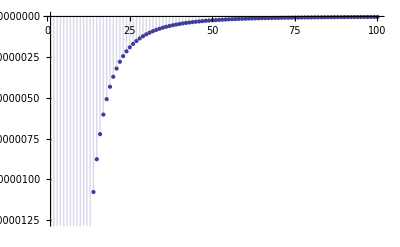

```mathematica
DiscretePlot[Re@vb6[n,.3+.7I],{n,1,100}]
```

```mathematica
(ⅈ √(1/2- ⅈ s))/(√(1/2+ ⅈ s))/.s->.3
```

0.514496+0.857493 ⅈ

```mathematica
TrigToExp[ArcTan[2s]]
```

1/2 ⅈ Log[1-2 ⅈ s]-1/2 ⅈ Log[1+2 ⅈ s]

```mathematica
1/2 ⅈ Log[1-2 ⅈ s]-1/2 ⅈ Log[1+2 ⅈ s]/.s->.3+.4I
```

0.785398+0.549306 ⅈ

```mathematica
1/2 ⅈ Log[1/2- ⅈ s]-1/2 ⅈ Log[1/2+ ⅈ s]/.s->.3+.4I
```

0.785398+0.549306 ⅈ

```mathematica
1/2 ⅈ Log[(1/2- ⅈ s)/(1/2+ ⅈ s)]
```

1/2 ⅈ Log[(1/2-ⅈ s)/(1/2+ⅈ s)]

```mathematica
Expand[(1-2s I)(1+2s I)]
```

1+4 s^2

```mathematica
vb7x[n_,s_]:=I((√(1/2- ⅈ s))/(√(1/2+ ⅈ s))n^(1/2+s I)Zeta[1/2+s I]-(√(1/2+ ⅈ s))/(√(1/2- ⅈ s))n^(1/2-s I)Zeta[1/2-s I])
vb7x2[n_,s_]:=I( E^(-I ArcTan[2s])n^(1/2+s I)Zeta[1/2+s I]-E^(I ArcTan[2s])n^(1/2-s I)Zeta[1/2-s I])
vb7x3[s_]:=I( E^(-I ArcTan[2s])Zeta[1/2+s I]-E^(I ArcTan[2s])Zeta[1/2-s I])
```

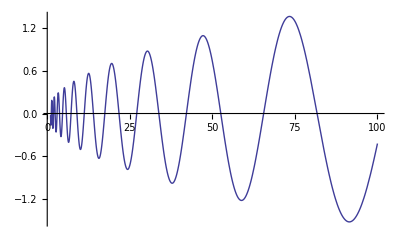

```mathematica
Plot[Re@vb7x2[n,N@Im@ZetaZero@1+.1],{n,1,100}]
```

```mathematica
vb7x3[N@Im@ZetaZero@1+.1I]
```

-0.00610065-0.0305753 ⅈ

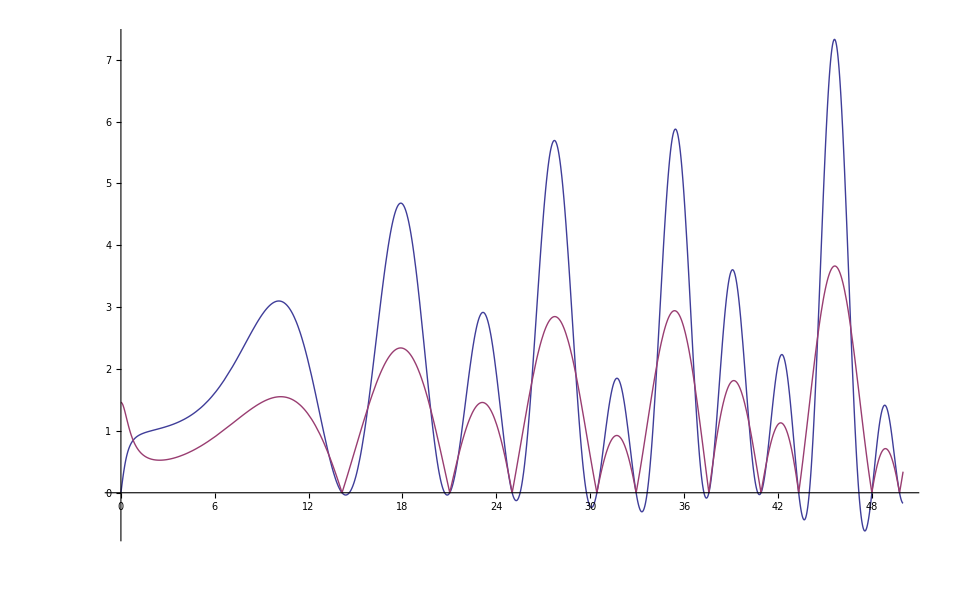

```mathematica
Plot[{Re@vb7x3[n], Abs@Zeta[.5+n I]},{n,0,50}]
```

```mathematica
FullSimplify[(2 (-2 s Cos[c]+Sin[c]))/(1+4 s^2)]
```

(2 (-2 s Cos[c]+Sin[c]))/(1+4 s^2)

```mathematica
-(4 s Cos[c])/(1+4 s^2)+(2 Sin[c])/(1+4 s^2)/.c->12.3/.s->7.2
```

-0.135874

```mathematica
-(4 s Cos[c])/(1+4 s^2)+Sin[c]/((1/2-s I)(1/2+s I))/.c->12.3/.s->7.2
```

-0.138401+0. ⅈ

```mathematica
(2 (-2 s Cos[c]+Sin[c]))/(1+4 s^2)/.c->Pi/2
```

2/(1+4 s^2)